Diplomado En Programación Básica
Universidad Autónoma de Chiapas
Centro Mesoamericano de Física Teórica

Michael S. Paucar R.

# MATHEMATICA Simulador del protocolo de criptografía cuántica BB84 con clasificador para detección de espionaje

Diciembre 2025

## 1. Introducción

Simulador interactivo del protocolo cuántico BB84 en Wolfram Languaje con integración de un clasificador basado en árboles de decisión para detectar espionaje a partir del QBER.

La herramienta permite ajustar parámetros como el número de qubits y la probabilidad de interceptación, generando visualizaciones 2D y 3D que muestran el comportamiento del protocolo bajo distintos niveles de perturbación. El objetivo es demostrar cómo los principios cuánticos y las técnicas de aprendizaje automático pueden combinarse para analizar la seguridad de un canal cuántico frente a ataques de tipo intercept–resend.

## 2. Objetivo

Desarrollar un simulador interactivo del protocolo BB84 en Wolfram Mathematica que permita visualizar la transmisión y medición de qubits, estimar el QBER bajo distintos niveles de perturbación y detectar intentos de espionaje mediante un clasificador supervisado basado en el análisis de errores.

## 3. Contenidos

Introducción

Objetivo

Contenidos

Antecedentes

Términos Clave

Desarrollo del Código

Preparación de Bits y Bases por Alice

Medición y Posible Espionaje por Bob

Simulación Principal del Protocolo BB84

Entrada de Parámetros por Usuario

Ejecución de la Simulación y Visualización Inicial

Generación de Datos para Entrenamiento del Clasificador IA

Chequeo de Clases Múltiples en Datos

Entrenamiento del Clasificador Ligero

Clasificación de la Simulación Actual

Resultados

Visualización QBER vs. Corridas

Distribución de Errores

Superficie 3D de QBER Promedio vs. N y p_eve

Distribución 3D de QBER vs. p_eve

Dispersión 3D Mejorada de Errores

Conclusiones

Recomendaciones

Bibliografía

## 4. Antecedentes

La computación cuántica amenaza la criptografía clásica, lo que impulsa el uso de protocolos como BB84, basado en qubits y en el principio de no clonación.

Cualquier medición no autorizada altera el estado cuántico y aumenta el QBER, permitiendo detectar espionaje.

La simulación en Mathematica facilita estudiar este comportamiento e integrar clasificadores ligeros para identificar intrusiones automáticamente.

## 5. Términos Clave

Qubit: Unidad básica de información cuántica, equivalente cuántico al bit clásico. Puede existir en superposición de estados 0 y 1, permitiendo cálculos paralelos en computación cuántica.

Eve: Eavesdropper o espía en escenarios criptográficos, como en BB84, quien intenta interceptar la comunicación entre Alice y Bob sin ser detectada, pero introduce perturbaciones detectables por principios cuánticos.

BB84: Protocolo de distribución de claves cuánticas propuesto por Bennett y Brassard en 1984, que usa qubits en bases rectilínea (+) y diagonal (x) para generar claves seguras, detectando espionaje vía elevación de QBER.

QBER (Quantum Bit Error Rate): Proporción de discrepancias entre los bits sifted de Alice y Bob. Valores altos (≈0.11–0.15 o más) indican posible intervención de un atacante y requieren abortar la clave

Sifting: Fase en QKD donde Alice y Bob comparan bases públicamente y retienen solo bits con bases coincidentes (~50% de los enviados), formando la clave raw.

Quantum Key Distribution (QKD): Método seguro para distribuir claves criptográficas usando mecánica cuántica, garantizando detección de eavesdroppers por teorema de no-clonación.

## 6. Desarrollo del Código

### 6.1 Preparación de Bits y Bases por Alice

```mathematica
(*Representación del Bit Clásico*)Graphics[{Text["0",{0,0}],(*Representa el estado 0*)Text["1",{1,0}] (*Representa el estado 1*)},PlotRange->{{-1.5,1.5},{-1.5,1.5}},Axes->True,AxesOrigin->{0,0},AxesLabel->{"Estado","Valor"},AspectRatio->1]
```

Qubit definido como unidad de información cuántica que puede prepararse en bases rectilínea (+) o diagonal (×)

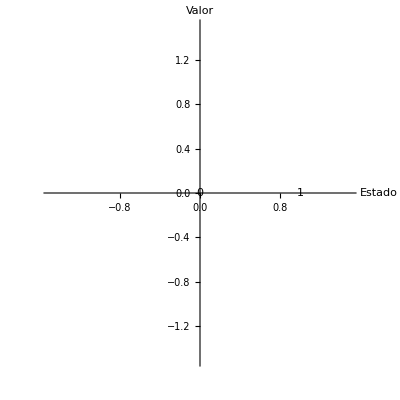

En el código alicePrep[n] se generan bits aleatorios y la base asociada para cada qubit, reproduciendo la preparación de estado de Alice

```mathematica
(*Representación de un qubit en la esfera de Bloch*)blochSphere[theta_,phi_]:=Graphics3D[{Sphere[{0,0,0},1],(*Esfera de Bloch*)(*Estado|0⟩ en el eje Z*)Red,PointSize[Large],Point[{0,0,1}],(*Estado|0⟩ en la parte superior de la esfera*)(*Estado|1⟩ en el eje Z*)Blue,Point[{0,0,-1}],(*Estado|1⟩ en la parte inferior de la esfera*)(*Superposición (representada por un punto en la esfera)*)Green,Point[{Sin[theta]*Cos[phi],Sin[theta]*Sin[phi],Cos[theta]}],(*Ejes X,Y,Z*)Black,Line[{{-1,0,0},{1,0,0}}],Line[{{0,-1,0},{0,1,0}}],Line[{{0,0,-1},{0,0,1}}]},PlotRange->{{-1.5,1.5},{-1.5,1.5},{-1.5,1.5}},Axes->True,AxesOrigin->{0,0,0},AxesLabel->{"X","Y","Z"},AspectRatio->1]

(*Parámetros para la superposición de un qubit en estado H (Hadamard)*)
theta=Pi/2;  (*Ángulo para la superposición*)
phi=Pi/2;    (*Ángulo de fase*)

(*Dibujar la esfera de Bloch con un qubit en superposición*)
blochSphere[theta,phi]
```

-Graphics3D-

# Función para Alice (EMISOR)

	1. Genera n bits aleatorios (0 o 1).
	2. Genera n bases aleatorias (+ o x).
	3. Devuelve ambas secuencias como un par: primero los bits y luego las bases.

```mathematica
(*Generar bits y bases aleatorias para Alice*)alicePrep[n_]:=Module[{bits,bases},bits=RandomChoice[{0,1},n];
(*Bits aleatorios*)bases=RandomChoice[{"+","x"},n];
(*Bases rectilínea (+) o diagonal (x)*){bits,bases}]
```

### 6.2 Medición y Posible Espionaje por Bob

Medir un qubit colapsa su estado y solo es determinado si la base del medidor coincide con la del emisor

```mathematica
(*Número de bits*)n=10;

(*Simulación de los valores de Alice y bases aleatorias*)
aliceBits=RandomChoice[{0,1},n];  (*Bits de Alice*)
aliceBases=RandomChoice[{"+","x"},n];  (*Bases de Alice*)

(*Bases de Bob aleatorias*)
bobBases=RandomChoice[{"+","x"},n];  (*Bases de Bob*)

(*Simulamos los bits de Bob basados en las bases*)
bobBits=Table[effectiveBit=aliceBits[[i]];
effectiveBasis=aliceBases[[i]];
(*Bob mide basado en su base y el qubit efectivo*)If[bobBases[[i]]==effectiveBasis,effectiveBit,RandomChoice[{0,1}]],{i,1,n}];

(*Generamos la tabla de Alice,Bob y sus bits y bases*)
table=Table[{"Alice ("<>ToString[i]<>")",aliceBits[[i]],aliceBases[[i]],bobBases[[i]],bobBits[[i]]},{i,1,n}];

(*Mostrar la tabla*)
Grid[Prepend[table,{"","Alice (Valor)","Alice (Base)","Bob (Base)","Bob (Valor)"}],Spacings->{2,1},Frame->All,Background->{None,{LightYellow,LightCyan}},ItemStyle->{FontSize->12}]
```

| Alice (Valor) | Alice (Base) | Bob (Base) | Bob (Valor)
Alice (1) | 0 | + | + | 0
Alice (2) | 1 | x | x | 1
Alice (3) | 1 | + | + | 1
Alice (4) | 1 | x | x | 1
Alice (5) | 1 | + | x | 0
Alice (6) | 1 | x | + | 0
Alice (7) | 0 | + | + | 0
Alice (8) | 1 | + | x | 1
Alice (9) | 1 | + | x | 1
Alice (10) | 0 | x | + | 1

bobMeasure selecciona bases para Bob y modela a Eve con probabilidad pEve, cuando Eve mide reenvía un fotón que puede introducir errores

```mathematica
(*Número de bits*)n=10;

(*Simulación de los valores de Alice y bases aleatorias*)
aliceBits=RandomChoice[{0,1},n];  (*Bits de Alice*)
aliceBases=RandomChoice[{"+","x"},n];  (*Bases de Alice*)

(*Bases de Bob aleatorias*)
bobBases=RandomChoice[{"+","x"},n];  (*Bases de Bob*)

(*Parámetro de intervención de Eve*)
pEve=0.5;  (*Probabilidad de que Eve intervenga*)

(*Simulamos los bits de Bob basados en las bases y la intervención de Eve*)
bobBits=Table[(*Inicializamos las variables de intervención*)effectiveBit=aliceBits[[i]];
effectiveBasis=aliceBases[[i]];
eveBase=RandomChoice[{"+","x"}];(*Base de Eve*)eveBit=RandomChoice[{0,1}];(*Valor que Eve podría medir*)(*Si Eve mide,alteramos el bit de Alice dependiendo de las bases*)If[RandomReal[]<pEve,(*Eve mide el qubit de Alice y puede introducir un error*)effectiveBit=If[eveBase==aliceBases[[i]],aliceBits[[i]],eveBit];
effectiveBasis=eveBase; (*Eve elige su propia base para el reenvío*)];
(*Bob mide el bit basado en la base que elige*)If[bobBases[[i]]==effectiveBasis,effectiveBit,RandomChoice[{0,1}]],{i,1,n}];

(*Generamos la tabla con los valores de Alice,Bob y Eve*)
table=Table[{"Alice ("<>ToString[i]<>")",aliceBits[[i]],aliceBases[[i]],RandomChoice[{"+","x"}],eveBits[[i]],bobBases[[i]],bobBits[[i]]},{i,1,n}];

(*Mostrar la tabla*)
Grid[Prepend[table,{"","Alice (Valor)","Alice (Base)","Eve (Base)","Eve (Valor)","Bob (Base)","Bob (Valor)"}],Spacings->{2,1},Frame->All,Background->{None,{LightYellow,LightCyan}},ItemStyle->{FontSize->12}]
```

| Alice (Valor) | Alice (Base) | Eve (Base) | Eve (Valor) | Bob (Base) | Bob (Valor)
Alice (1) | 0 | + | + | 0 | + | 0
Alice (2) | 1 | + | x | 1 | + | 1
Alice (3) | 0 | x | x | 1 | + | 1
Alice (4) | 1 | + | x | 1 | + | 1
Alice (5) | 1 | x | x | 0 | + | 1
Alice (6) | 0 | x | + | 0 | x | 0
Alice (7) | 0 | + | x | 1 | + | 0
Alice (8) | 0 | + | + | 1 | x | 0
Alice (9) | 0 | + | x | 1 | x | 1
Alice (10) | 0 | x | + | 0 | x | 0

# Función para Bob (RECEPTOR)

	1. Bob elige bases aleatorias para medir los bits enviados por Alice.
	2. Si Eve está presente, ella mide los bits de Alice con una base aleatoria y reenvía los bits a Bob en su propia base. Si las bases coinciden, Bob obtiene el valor correcto del bit, de lo contrario, obtiene un valor aleatorio.
	3. Si Eve no está presente, Bob mide los bits directamente en las bases que él eligió.
	4. La función devuelve los bits medidos por Bob y las bases que usó.

```mathematica
(*Elegir bases aleatorias y medir*)bobMeasure[aliceBits_,aliceBases_,n_,evePresent_,pEve_]:=Module[{bobBases,bobBits,i,effectiveBit,effectiveBasis,eveBasis,eveBit},bobBases=RandomChoice[{"+","x"},n];
bobBits=Table[effectiveBit=aliceBits[[i]];
effectiveBasis=aliceBases[[i]];
If[RandomReal[]<pEve&&evePresent,(*Elige base aleatoria independiente*)eveBasis=RandomChoice[{"+","x"}];
(*Eve mide:Correcto si bases coinciden,aleatorio si no*)eveBit=If[eveBasis==aliceBases[[i]],aliceBits[[i]],RandomChoice[{0,1}]];
(*Reenvía en su base:Bob ve el bit efectivo de Eve en base de Eve*)effectiveBit=eveBit;
effectiveBasis=eveBasis;];
(*Bob mide basado en el qubit efectivo:Correcto si sus bases coinciden,aleatorio si no no coinden*)If[bobBases[[i]]==effectiveBasis,effectiveBit,RandomChoice[{0,1}]],{i,1,n}];
{bobBits,bobBases}]
```

### 6.3 Simulación Principal del Protocolo BB84

Sifting conserva solo los bits donde Alice y Bob usaron la misma base para formar la clave filtrada

```mathematica
(*Número de bits*)n=10;

(*Simulación de los valores de Alice y bases aleatorias*)
aliceBits=RandomChoice[{0,1},n];  (*Bits de Alice*)
aliceBases=RandomChoice[{"+","x"},n];  (*Bases de Alice*)

(*Bases de Bob aleatorias*)
bobBases=RandomChoice[{"+","x"},n];  (*Bases de Bob*)

(*Parámetro de intervención de Eve*)
pEve=0.5;  (*Probabilidad de que Eve intervenga*)

(*Simulamos los bits de Bob basados en las bases y la intervención de Eve*)
bobBits=Table[(*Inicializamos las variables de intervención*)effectiveBit=aliceBits[[i]];
effectiveBasis=aliceBases[[i]];
eveBase=RandomChoice[{"+","x"}];(*Base de Eve*)eveBit=RandomChoice[{0,1}];(*Valor que Eve podría medir*)(*Determinamos los casos*)case="";(*Inicializamos el caso*)(*Caso 1:Eve acierta y Bob recupera el estado original*)If[RandomReal[]<pEve,If[eveBase==aliceBases[[i]],(*Eve mide correctamente*)effectiveBit=aliceBits[[i]];
effectiveBasis=eveBase;
case="Caso 1: Eve acierta y Bob recupera el estado original.";],case="";  (*No interviene Eve*)];
(*Caso 2:Eve intercepta,cambia el estado y Bob no acierta*)If[case==""&&RandomReal[]<pEve,If[eveBase!=aliceBases[[i]],(*Eve mide y cambia el estado*)effectiveBit=eveBit;
effectiveBasis=eveBase;
case="Caso 2: Eve cambia el estado y Bob no acierta.";]];
(*Caso 3:Alice detecta la interferencia de Eve y Bob no acierta*)If[case==""&&RandomReal[]<pEve,case="Caso 3: Alice detecta la interferencia y Bob no acierta.";];
(*Caso 4:Alice,Eve y Bob coinciden (sin errores)*)If[case=="",case="Caso 4: Alice, Eve y Bob coinciden sin errores."];
(*Bob mide el bit basado en la base que elige*)If[bobBases[[i]]==effectiveBasis,effectiveBit,RandomChoice[{0,1}]],{i,1,n}];

(*Generamos la tabla con los valores de Alice,Bob y Eve y sus colores*)
table=Table[{"Alice ("<>ToString[i]<>")",aliceBits[[i]],aliceBases[[i]],RandomChoice[{"+","x"}],eveBits[[i]],bobBases[[i]],bobBits[[i]],case},{i,1,n}];

(*Colores para cada caso*)
caseColors=<|"Caso 1: Eve acierta y Bob recupera el estado original."->LightGreen,"Caso 2: Eve cambia el estado y Bob no acierta."->LightCoral,"Caso 3: Alice detecta la interferencia y Bob no acierta."->LightYellow,"Caso 4: Alice, Eve y Bob coinciden sin errores."->LightCyan|>;

(*Mostrar la tabla con colores según el caso*)
Grid[Prepend[table,{"","Alice (Valor)","Alice (Base)","Eve (Base)","Eve (Valor)","Bob (Base)","Bob (Valor)","Caso"}],Spacings->{2,1},Frame->All,Background->Table[caseColors[table[[i,8]]],{i,1,n}],ItemStyle->{FontSize->12}]
```

| Alice (Valor) | Alice (Base) | Eve (Base) | Eve (Valor) | Bob (Base) | Bob (Valor) | Caso
Alice (1) | 0 | x | x | eveBits⟦1⟧ | + | 1 | Caso 4: Alice, Eve y Bob coinciden sin errores.
Alice (2) | 0 | + | + | eveBits⟦2⟧ | + | 0 | Caso 4: Alice, Eve y Bob coinciden sin errores.
Alice (3) | 1 | x | x | eveBits⟦3⟧ | + | 1 | Caso 4: Alice, Eve y Bob coinciden sin errores.
Alice (4) | 1 | + | + | eveBits⟦4⟧ | + | 1 | Caso 4: Alice, Eve y Bob coinciden sin errores.
Alice (5) | 1 | x | + | eveBits⟦5⟧ | x | 1 | Caso 4: Alice, Eve y Bob coinciden sin errores.
Alice (6) | 1 | x | + | eveBits⟦6⟧ | x | 1 | Caso 4: Alice, Eve y Bob coinciden sin errores.
Alice (7) | 1 | + | x | eveBits⟦7⟧ | x | 1 | Caso 4: Alice, Eve y Bob coinciden sin errores.
Alice (8) | 1 | + | + | eveBits⟦8⟧ | x | 0 | Caso 4: Alice, Eve y Bob coinciden sin errores.
Alice (9) | 1 | + | + | eveBits⟦9⟧ | x | 1 | Caso 4: Alice, Eve y Bob coinciden sin errores.
Alice (10) | 1 | + | + | eveBits⟦10⟧ | + | 1 | Caso 4: Alice, Eve y Bob coinciden sin errores.

simulateBB84 realiza preparación, medición, sifting y calcula el QBER sobre un subconjunto de la clave para estimar perturbaciones

QBER=Nerrores_bit/Ntotal_bit

El QBER es: 0.333333

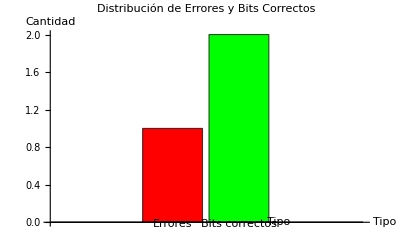

Part::partd: Part specification eveBits⟦1⟧ is longer than depth of object.

Part::partd: Part specification eveBits⟦2⟧ is longer than depth of object.

Part::partd: Part specification eveBits⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

| Alice (Valor) | Alice (Base) | Eve (Base) | Eve (Valor) | Bob (Base) | Bob (Valor) | Caso
Alice (1) | 1 | + | x | eveBits⟦1⟧ | + | 0 | Caso 3: Alice detecta la interferencia y Bob no acierta.
Alice (2) | 1 | x | x | eveBits⟦2⟧ | + | 1 | Caso 3: Alice detecta la interferencia y Bob no acierta.
Alice (3) | 1 | x | x | eveBits⟦3⟧ | x | 1 | Caso 3: Alice detecta la interferencia y Bob no acierta.
Alice (4) | 0 | + | + | eveBits⟦4⟧ | + | 0 | Caso 3: Alice detecta la interferencia y Bob no acierta.
Alice (5) | 0 | + | x | eveBits⟦5⟧ | + | 0 | Caso 3: Alice detecta la interferencia y Bob no acierta.
Alice (6) | 0 | + | x | eveBits⟦6⟧ | + | 0 | Caso 3: Alice detecta la interferencia y Bob no acierta.
Alice (7) | 1 | x | + | eveBits⟦7⟧ | + | 0 | Caso 3: Alice detecta la interferencia y Bob no acierta.
Alice (8) | 0 | x | x | eveBits⟦8⟧ | x | 1 | Caso 3: Alice detecta la interferencia y Bob no acierta.
Alice (9) | 1 | x | + | eveBits⟦9⟧ | + | 0 | Caso 3: Alice detecta la interferencia y Bob no acierta.
Alice (10) | 0 | x | + | eveBits⟦10⟧ | x | 0 | Caso 3: Alice detecta la interferencia y Bob no acierta.

```mathematica
(*Simulación de BB84 con cálculo de QBER*)(*Número de bits*)n=10;

(*Simulación de los valores de Alice y bases aleatorias*)
aliceBits=RandomChoice[{0,1},n];  (*Bits de Alice*)
aliceBases=RandomChoice[{"+","x"},n];  (*Bases de Alice*)

(*Bases de Bob aleatorias*)
bobBases=RandomChoice[{"+","x"},n];  (*Bases de Bob*)

(*Parámetro de intervención de Eve*)
pEve=0.5;  (*Probabilidad de que Eve intervenga*)

(*Simulamos los bits de Bob basados en las bases y la intervención de Eve*)
bobBits=Table[(*Inicializamos las variables de intervención*)effectiveBit=aliceBits[[i]];
effectiveBasis=aliceBases[[i]];
eveBase=RandomChoice[{"+","x"}];(*Base de Eve*)eveBit=RandomChoice[{0,1}];(*Valor que Eve podría medir*)(*Determinamos los casos*)case="";(*Inicializamos el caso*)(*Caso 1:Eve acierta y Bob recupera el estado original*)If[RandomReal[]<pEve,If[eveBase==aliceBases[[i]],(*Eve mide correctamente*)effectiveBit=aliceBits[[i]];
effectiveBasis=eveBase;
case="Caso 1: Eve acierta y Bob recupera el estado original.";],case="";  (*No interviene Eve*)];
(*Caso 2:Eve intercepta,cambia el estado y Bob no acierta*)If[case==""&&RandomReal[]<pEve,If[eveBase!=aliceBases[[i]],(*Eve mide y cambia el estado*)effectiveBit=eveBit;
effectiveBasis=eveBase;
case="Caso 2: Eve cambia el estado y Bob no acierta.";]];
(*Caso 3:Alice detecta la interferencia de Eve y Bob no acierta*)If[case==""&&RandomReal[]<pEve,case="Caso 3: Alice detecta la interferencia y Bob no acierta.";];
(*Caso 4:Alice,Eve y Bob coinciden (sin errores)*)If[case=="",case="Caso 4: Alice, Eve y Bob coinciden sin errores."];
(*Bob mide el bit basado en la base que elige*)If[bobBases[[i]]==effectiveBasis,effectiveBit,RandomChoice[{0,1}]],{i,1,n}];

(*Realizamos el proceso de sifting:filtramos donde las bases coinciden*)
siftedKeyAlice={};
siftedKeyBob={};
Do[If[aliceBases[[i]]==bobBases[[i]],AppendTo[siftedKeyAlice,aliceBits[[i]]];
AppendTo[siftedKeyBob,bobBits[[i]]]],{i,1,n}];

(*Calculamos el QBER:número de errores sobre el total de bits en el subconjunto de verificación*)
halfLen=Floor[Length[siftedKeyAlice]/2];
If[halfLen==0,qber=0,errors=Count[Take[siftedKeyAlice,halfLen]-Take[siftedKeyBob,halfLen],x_/;x!=0];
qber=N[errors/halfLen];];

(*Mostrar QBER en texto*)
Print["El QBER es: ",qber];

(*Graficar el QBER:representación visual de los errores*)
BarChart[{errors,halfLen-errors},ChartLabels->{"Errores","Bits correctos"},ChartStyle->{Red,Green},PlotLabel->"Distribución de Errores y Bits Correctos",AxesLabel->{"Tipo","Cantidad"}]

(*Mostrar la tabla con los valores de Alice,Bob y Eve y los casos*)
table=Table[{"Alice ("<>ToString[i]<>")",aliceBits[[i]],aliceBases[[i]],RandomChoice[{"+","x"}],eveBits[[i]],bobBases[[i]],bobBits[[i]],case},{i,1,n}];

(*Colores para cada caso*)
caseColors=<|"Caso 1: Eve acierta y Bob recupera el estado original."->LightGreen,"Caso 2: Eve cambia el estado y Bob no acierta."->LightCoral,"Caso 3: Alice detecta la interferencia y Bob no acierta."->LightYellow,"Caso 4: Alice, Eve y Bob coinciden sin errores."->LightCyan|>;

(*Mostrar la tabla con colores según el caso*)
Grid[Prepend[table,{"","Alice (Valor)","Alice (Base)","Eve (Base)","Eve (Valor)","Bob (Base)","Bob (Valor)","Caso"}],Spacings->{2,1},Frame->All,Background->Table[caseColors[table[[i,8]]],{i,1,n}],ItemStyle->{FontSize->12}]
```

# Preparación, medición, sifting y cálculo de QBER

	1. Preparación de Alice: Alice prepara n bits y elige bases aleatorias.
	2. Medición de Bob: Bob mide los bits que recibe de Alice con sus propias bases aleatorias.
	3. Sifting: Alice y Bob descartan los bits donde sus bases no coincidieron, y se quedan solo con aquellos bits donde las bases coincidieron.
	4. Chequeo de errores: Se calcula la tasa de error cuántico (qber) comparando un subconjunto de bits de la clave.

Resultado: Se devuelve la clave de Alice (siftedKeyAlice), la clave de Bob (siftedKeyBob), y el QBER calculado.

```mathematica
(*Función principal de simulación BB84*)
simulateBB84[n_,pEve_,evePresent_]:=Module[{alice,bob,siftedKeyAlice,siftedKeyBob,errors,qber},alice=alicePrep[n];
bob=bobMeasure[alice[[1]],alice[[2]],n,evePresent,pEve];

(*Sifting:Mantener bits donde bases coinciden*)
siftedKeyAlice={};
siftedKeyBob={};
Do[If[alice[[2,i]]==bob[[2,i]],AppendTo[siftedKeyAlice,alice[[1,i]]];
AppendTo[siftedKeyBob,bob[[1,i]]]],{i,1,n}];

(*Calcular errores en subconjunto de chequeo (mitad de la clave sifted)*)halfLen=Floor[Length[siftedKeyAlice]/2];
If[halfLen==0,qber=0,errors=Count[Take[siftedKeyAlice,halfLen]-Take[siftedKeyBob,halfLen],x_/;x!=0];
qber=N[errors/halfLen];];
{siftedKeyAlice,siftedKeyBob,qber}]
```

### 6.4 Entrada de Parámetros por Usuario

# No valido enteros positivos
	1. Usuario ingresa un número de qubits: 1000
	2. Usuario ingresa la probabilidad de espionaje: 0.1
	3. Usuario decide si desea simular el espionaje: True

Parámetros clave: número de qubits n, probabilidad de ataque pEve y flag evePresent para activar la simulación de Eve

Los Input permiten experimentar con distintas condiciones y observar efectos estadísticos

```mathematica
(*Entrada de parámetros por usuario*)n=Input["Ingrese el número de qubits (N, e.g., 1000): "];
pEve=Input["Ingrese la probabilidad de espionaje (p_eve, entre 0 y 1): "];
evePresent=Input["¿Simular espionaje? (True/False): "];
```

### 6.5 Ejecución de la Simulación y Visualización Inicial

Salida inmediata : claves sifted de Alice y Bob y el QBER estimado para la corrida actual

# Llama a simulateBB84 y los parámetros

```mathematica
(*Ejecutar simulación*)result=simulateBB84[n,pEve,evePresent];
```

Imprimir los primeros elementos ayuda a verificar  visualmente el comportamiento del protocolo

# Muestra claves sifted, se puede cambiar acorde n ingresado por el usuario

```mathematica
(*Muestra primeros 10 claves*)
Print["Clave sifted de Alice: ",Take[result[[1]],100]];  
Print["Clave sifted de Bob: ",Take[result[[2]],10]];
Print["Tasa de error cuántico (QBER): ",result[[3]]];
```

Take::take: Cannot take positions 1 through 100 in {1,1,0,1,0,0,1,1,1,1,0,1,1,1,1,1,0,0,1,0,0,1,1,0,1,0,1,1,1,1,0,1,0,1,1,0,1,1,0,1,0,1,1,1,0,0}.

Clave sifted de Alice: Take[{1,1,0,1,0,0,1,1,1,1,0,1,1,1,1,1,0,0,1,0,0,1,1,0,1,0,1,1,1,1,0,1,0,1,1,0,1,1,0,1,0,1,1,1,0,0},100]

Clave sifted de Bob: {1,1,0,1,1,0,1,1,1,1}

Tasa de error cuántico (QBER): 0.217391

### 6.6 Generación de Datos para Entrenamiento del Clasificador IA

Se generan simulaciones balanceadas con y sin espionaje para construir un dataset supervisado

```mathematica
(*Generamos 10 valores de QBER aleatorios*)n=10;
qberNoEspionaje=RandomReal[{0,0.1},5]; (*QBER bajo para No Espionaje*)
qberEspionaje=RandomReal[{0.15,1},5]; (*QBER alto para Espionaje Detectado*)

(*Crear los datos con clases:1 para No Espionaje,2 para Espionaje Detectado*)
data=Join[Table[{qberNoEspionaje[[i]],"No Espionaje"},{i,1,Length[qberNoEspionaje]}],(*No Espionaje*)Table[{qberEspionaje[[i]],"Espionaje Detectado"},{i,1,Length[qberEspionaje]}] (*Espionaje Detectado*)];

(*Crear la tabla con encabezados*)
Grid[Prepend[data,{"QBER","Clase"}],Frame->All,Spacings->{2,1},Background->{None,{LightYellow,LightCyan}},ItemStyle->{FontSize->12}]
```

QBER | Clase
0.0948088 | No Espionaje
0.0694316 | No Espionaje
0.0534292 | No Espionaje
0.058639 | No Espionaje
0.0183274 | No Espionaje
0.73858 | Espionaje Detectado
0.350756 | Espionaje Detectado
0.173583 | Espionaje Detectado
0.332891 | Espionaje Detectado
0.97371 | Espionaje Detectado

Etiquetado simple: No Espionaje y Espionaje Detectado usando un umbral de QBER (e.g. 0.15) para entrenamiento

# Crea dataset balanceado (50 sin/50 con Eve)

```mathematica
(*Generar datos para entrenamiento del clasificador IA-Balanceado para asegurar clases*)
data=Join[Table[Module[{qber},qber=simulateBB84[n,pEve,False][[3]];

{qber}->"No Espionaje"],{50}  (*50 sin Eve:QBER bajo*)],Table[Module[{qber},qber=simulateBB84[n,pEve,True][[3]];
{qber}->If[qber>0.15,"Espionaje Detectado","No Espionaje"]  (*Umbral para simulacion depende de otros factores*)],
{50}  (*50 con Eve:QBER alto si pEve suficiente*)]];
```

### 6.7 Chequeo de Clases Múltiples en Datos

Verificar que el dataset contenga al menos dos clases evita entrenar un modelo inválido

El chequeo con Union[Values[data]] emite advertencia si falta diversidad de clases

# Usa Union para verificar clases: imprime advertencia si una sola, evitando error en entrenamiento

```mathematica
(*Verifico para asegurar múltiples clases*)classes=Union[Values[data]];
If[Length[classes]<2,Print["Advertencia: Solo una clase en datos. Aumenta pEve o baja umbral."]];
```

### 6.8 Entrenamiento del Clasificador Ligero

Clasificador interpretable DecisionTree entrenado con Classify[data, Method -> “DecisionTree”]

Aprovecha la simplicidad del QBER como característica para una detección rápida y explicable

# Entrena con Classify[Method->”DecisionTree”]

```mathematica
(*Entrenar clasificador ligero:Árbol de decisión*)classifier=Classify[data,Method->"DecisionTree"];
```

```mathematica
%15
```

ClassifierFunction[…]

```mathematica
%182
```

ClassifierFunction[…]

```mathematica
%163
```

ClassifierFunction[…]

```mathematica
%422
```

ClassifierFunction[…]

### 6.9 Clasificación de la Simulación Actual

Se evalúa la corrida actual pasando su QBER al clasificador y mostrando la predicción

prediction = classifier[{result[[3]]}] devuelve No Espionaje o Espionaje Detectado según el modelo

# Aplica clasificador a QBER actual

```mathematica
(*Clasificar la simulación actual*)prediction=classifier[{result[[3]]}];
Print["Predicción del clasificador IA: ",prediction];
```

Predicción del clasificador IA: Espionaje Detectado

## 7. Resultados

### 7.1 Visualización QBER vs. Corridas

# Al mover el deslizante de p_eve, puedes ver cómo cambia la tasa de error cuántico (QBER) al variar la probabilidad de espionaje.

```mathematica
(*Visualización  2D *)Manipulate[Module[{qbers},qbers=Table[simulateBB84[n,p,True][[3]],{10}];
ListPlot[qbers,PlotLabel->Style["QBER vs. Corrida (con Espionaje)",Bold,14],Frame->True,FrameLabel->{Style["Número de Corrida",Bold],Style["QBER",Bold]},PlotStyle->Directive[Thick,ColorData["Rainbow"][p]],Filling->Axis,FillingStyle->Opacity[0.3],Joined->True,PlotLegends->BarLegend[{"Rainbow",{0,1}},LegendLabel->"p_eve"]]],{p,0,1,0.1},LabelStyle->Directive[Black,Bold]]
```

### 7.2 Distribución de Errores

# Visualizar cómo se distribuyen los valores de la tasa de error cuántico (QBER) en función de las simulaciones de BB84 con espionaje.

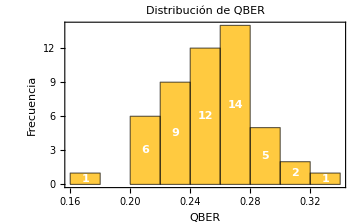

```mathematica
(*Distribución de errores*)errorDist=Table[simulateBB84[n,pEve,evePresent][[3]],{50}];
Histogram[errorDist,PlotLabel->Style["Distribución de QBER",Bold,14],Frame->True,FrameLabel->{Style["QBER",Bold],Style["Frecuencia",Bold]},ChartStyle->Directive[EdgeForm[Thick],ColorData["DeepSeaColors"]],LabelingFunction->(Placed[Style[#1,White,Bold],Center]&),PlotRange->All,ImageSize->Medium]
```

### 7.3 QBER Promedio vs. N y p_eve

# Crear una superficie 3D que muestra el QBER promedio (tasa de error cuántico) en función de dos parámetros: el número de qubits nVal y la probabilidad de espionaje pVal

```mathematica
(*Superficie QBER promedio-Usando puntos explícitos para interpolación estructurada*)qberSurfaceDataPoints=Flatten[Table[{nVal,pVal,Mean[Table[simulateBB84[nVal,pVal,evePresent][[3]],{5}]]},{nVal,100,2000,200},{pVal,0,1,0.1}],1];
interFunc=Interpolation[qberSurfaceDataPoints,InterpolationOrder->2];  (*Orden como entero explícito*)
```

# Genera una visualización interactiva en 3D de la superficie de la tasa de error cuántico (QBER) promedio en función de dos parámetros: el número de qubits (N) y la probabilidad de espionaje (p_eve)

```mathematica
Manipulate[Plot3D[interFunc[nVal,pVal],{nVal,100,maxN},{pVal,0,1},PlotLabel->Style["Superficie 3D de QBER Promedio",Bold,14],AxesLabel->{Style["N (Qubits)",Bold],Style["p_eve",Bold],Style["QBER",Bold]},ColorFunction->"TemperatureMap",Mesh->{{0.15}},MeshStyle->Directive[Thick,Red],Lighting->"Neutral",PlotRange->{0,0.3},MaxRecursion->3,ImageSize->Large],{{maxN,2000,"Rango Máximo N"},1000,3000,500},{{evePresent,True,"Simular Espionaje"},{True,False}}]
```

### 7.4 QBER vs. p_eve

# genera una tabla de datos bivariados para una simulación de BB84 con espionaje (Eve)

```mathematica
(*Densidad 3D con Histogram3D de datos bivariados-Corregido binning y leyendas*)bivarData=Flatten[Table[{simulateBB84[n,pVar,evePresent][[3]],pVar},{pVar,0,1,0.05},{20}],1];
```

# Muestra la distribución de QBER en función de la probabilidad de espionaje (p_eve)

```mathematica
Manipulate[Histogram3D[bivarData,bins,"Count",PlotLabel->Style["Distribución 3D de QBER vs. p_eve",Bold,14],AxesLabel->{Style["QBER",Bold],Style["p_eve",Bold],Style["Frecuencia",Bold]},ColorFunction->"AvocadoColors",ChartLegends->Automatic,BoxRatios->{1,1,0.5},Lighting->"Neutral",ImageSize->Large],{{bins,20,"Número de Bins"},10,50,5}]
```

### 7.5 Dispersión 3D

# Genera un conjunto de datos para visualizar la dispersión 3D de la tasa de error cuántico (QBER) en función de dos parámetros: la probabilidad de espionaje (p_eve) y el número de corrida (runIdx).

```mathematica
(*Dispersión 3D*)multiRunData=Flatten[Table[{simulateBB84[n,p,evePresent][[3]],p,runIdx},{p,0,1,0.2},{runIdx,1,10}],1];
```

# Genera un conjunto de datos para visualizar la dispersión 3D de la tasa de error cuántico (QBER) en función de dos parámetros: la probabilidad de espionaje (p_eve) y el número de corrida (runIdx).

```mathematica
Manipulate[ListPointPlot3D[multiRunData,PlotStyle->Directive[PointSize[Medium],Opacity[opacity]],ColorFunction->(ColorData["SolarColors"][#1]&),AxesLabel->{Style["QBER",Bold],Style["p_eve",Bold],Style["Corrida",Bold]},PlotLabel->Style["Dispersión 3D de Errores",Bold,14],Filling->Axis,PlotRange->All,PlotLegends->BarLegend[{"SolarColors",{0,0.5}}],ImageSize->Large],{{opacity,0.8,"Opacidad"},0.5,1,0.1}]
```

## 8. Conclusiones

El protocolo BB84 permite detectar un Espía debido al aumento en la tasa de errores cuando se intercepta y reenvía información.

Un clasificador entrenado con datos sintéticos puede identificar con buena precisión escenarios con y sin ataque usando características sencillas (número de errores y tasa de error).

La implementación en Mathematica permite combinar simulación, visualización y técnicas de IA ligera de forma integrada y reproducible.

## 9. Recomendaciones

Incorporar ruido de canal realista para simular imperfecciones prácticas.

Extender a variantes como decoy-state BB84 contra ataques photon-number-splitting.

Añadir métricas de clasificador (ClassifierMeasurements para accuracy, confusion matrix).

Usar ParallelTable para optimizar simulaciones grandes.

Integrar QuantumFramework paclet de Wolfram para simulación cuántica genuina con gates.

Explorar redes neuronales en Mathematica para clasificadores más avanzados, comparando con DecisionTree.

## 10. Bibliografía

Bennett, C. H., & Brassard, G. (1984). Quantum Cryptography: Public Key Distribution and Coin Tossing. Proceedings of IEEE International Conference on Computers, Systems and Signal Processing.

Shor, P. W., & Preskill, J. (2000). Simple Proof of Security of the BB84 Quantum Key Distribution Protocol. Physical Review Letters, 85(2), 441-444.

Comprehensive Analysis of BB84, A Quantum Key Distribution Protocol. arXiv:2312.05609v1 (2023).

Wolfram Research. (2024). Classify - Wolfram Language Documentation. https://reference.wolfram.com/language/ref/Classify.html

Wolfram Research. (2024). DecisionTree - Wolfram Language Documentation. https://reference.wolfram.com/language/ref/method/DecisionTree.html

Wolfram Research. (2024). Manipulate - Wolfram Language Documentation. https://reference.wolfram.com/language/ref/Manipulate.html

Wolfram Research. (2024). Plot3D: Plot a Function in 3D

Wolfram Documentation. https://reference.wolfram.com/language/ref/Plot3D.html

Wolfram Research. (2024). Histogram: Plot data in bins - Wolfram Documentation. https://reference.wolfram.com/language/ref/Histogram.html

Wolfram Research. (2024). Histogram3D - Wolfram Language Documentation. https://reference.wolfram.com/language/ref/Histogram3D.htm

Wolfram Research. (2024). ListPointPlot3D - Wolfram Language Documentation. https://reference.wolfram.com/language/ref/ListPointPlot3D.html

Wolfram Research. (2024). RandomChoice - Wolfram Language Documentation. https://reference.wolfram.com/language/ref/RandomChoice.html

Wolfram Research. (2024). Table - Wolfram Language Documentation. https://reference.wolfram.com/language/ref/Table.html

Wolfram Research. (2024). If - Wolfram Language Documentation. https://reference.wolfram.com/language/ref/If.html

Wolfram Research. (2024). Input - Wolfram Language Documentation. https://reference.wolfram.com/language/ref/Input.html

Lecture Notes: Security Proofs of Quantum Key Distribution. (n.d.). https://glauciamg.github.io/assets/pdf/LectureNotes_SecurityQKD.pdf